In this note book the Vector tools by Dr. Alan A Barhorst was used. Please contact him via alan.barhorst@louisiana.edu for it. 
You can cite the work of this notebook using: 
Amarasiri, N., Barhorst, A. A., and Gottumukkala, R. (March 7, 2024). “Investigating Suitable Combinations of Dynamic Models and Control Techniques for Offline Reinforcement Learning Based Navigation: Application of Universal Omni-Wheeled Robots.” ASME. Letters Dyn. Sys. Control. April 2024; 4(2): 021007. https://doi.org/10.1115/1.4064517

This paper can be downloaded using https://www.researchgate.net/profile/Nalaka-Amarasiri

Please cite the vector tools by using:
Barhorst, A. A., 1997, “Symbolic Equation Processing Utilizing Vector/Dyad Notation,” J. Sound Vib., 208(5), pp. 823–839.

## Input the definitions for the vector operations

```mathematica
<<"/Users/nalakaamarasiri/Desktop/vectorDefsMM30.m" (*This is the vector tools by Dr. Alan A Barhorst. Please contact him from alan.barhorst@louisiana.edu*)
```

These Engineering Vector algorithms are copyright Alan A. Barhorst

## Define the symbols used for Unit Vectors and Unit Dyads

```mathematica
a[x_]:=unitVector[A,a,x]
b[x_]:=unitVector[B,b,x]
c[x_]:=unitVector[C,c,x]
d[x_]:=unitVector[D,d,x]
e[x_]:=unitVector[E,e,x]
f[x_]:=unitVector[F,f,x]
g[x_]:=unitVector[G,g,x]
h[x_]:=unitVector[H,h,x]
l[x_]:=unitVector[L,l,x]
m[x_]:=unitVector[M,m,x]
p[x_]:=unitVector[P,p,x]
s[x_]:=unitVector[S,s,x]
n[x_]:=unitVector[N,n,x]
w[x_]:=unitVector[W,w,x]
aa[x_,y_]:=unitDyad[a[x],a[y]]
bb[x_,y_]:=unitDyad[b[x],b[y]]
cc[x_,y_]:=unitDyad[c[x],c[y]]
dd[x_,y_]:=unitDyad[d[x],d[y]]
ee[x_,y_]:=unitDyad[e[x],e[y]]
ff[x_,y_]:=unitDyad[f[x],f[y]]
gg[x_,y_]:=unitDyad[g[x],g[y]]
hh[x_,y_]:=unitDyad[h[x],h[y]]
ll[x_,y_]:=unitDyad[l[x],l[y]]
mm[x_,y_]:=unitDyad[m[x],m[y]]
pp[x_,y_]:=unitDyad[p[x],p[y]]
ss[x_,y_]:=unitDyad[s[x],s[y]]
ww[x_,y_]:=unitDyad[w[x],w[y]]
```

## Robot graphic

-Graphics3D-

#### Base

```mathematica
vecL=3;
```

```mathematica
widthBase=8;depthBase=8;heightBase=1;
```

```mathematica
baseShape=Cuboid[
{-widthBase/2,-depthBase/2,-heightBase/2},
{widthBase/2,depthBase/2,heightBase/2}];
```

```mathematica
baseGraphic={{Opacity[1],baseShape},
{
		{AbsoluteThickness[1],RGBColor[1,0,0],Line[{{0,0,0},{vecL,0,0}}]},{AbsoluteThickness[1],RGBColor[0,1,0],Line[{{0,0,0},{0,vecL,0}}]},{AbsoluteThickness[1],RGBColor[0,0,1],Line[{{0,0,0},{0,0,vecL}}]}}};
```

```mathematica
Show[Graphics3D[baseGraphic],ViewPoint->{1,1,1},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All]
```

-Graphics3D-

#### 1st wheel

```mathematica
vecL=2;
```

```mathematica
halfHeightwheel=0.4;
wheelBase={0,0,-halfHeightwheel};
wheelTop={0,0,halfHeightwheel};
wheelRadius=3;
```

```mathematica
wheelshape1=Cylinder[{wheelBase,wheelTop},wheelRadius];
```

```mathematica
Show[Graphics3D[{Glow[Red],wheelshape1}],ViewPoint->{1,1,1},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All]
```

-Graphics3D-

```mathematica
wheelGraphic1={Rotate[{Opacity[0.1],wheelshape1},Pi/2,{0,1,0}],

		{AbsoluteThickness[1],RGBColor[1,0,0],Line[{{0,0,0},{vecL,0,0}}]},{AbsoluteThickness[1],RGBColor[0,1,0],Line[{{0,0,0},{0,vecL,0}}]},{AbsoluteThickness[1],RGBColor[0,0,1],Line[{{0,0,0},{0,0,vecL}}]}};
```

```mathematica
wheelGraphic11={Rotate[{Opacity[0.1],wheelshape1},Pi/2,{0,1,0}],

		{AbsoluteThickness[1],RGBColor[1,0,0],Line[{{0,0,0},{vecL,0,0}}]},{AbsoluteThickness[1],RGBColor[0,1,0],Line[{{0,0,0},{0,vecL,0}}]},{AbsoluteThickness[1],RGBColor[0,0,1],Line[{{0,0,0},{0,0,vecL}}]}};
Show[Graphics3D[{Glow[Red],wheelGraphic11}],ViewPoint->{1,1,1},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All]
```

-Graphics3D-

```mathematica
wheelGraphic1={Rotate[{Opacity[0.1],wheelGraphic11},Pi/2,{0,0,1}],

		{AbsoluteThickness[1],RGBColor[1,0,0],Line[{{0,0,0},{vecL,0,0}}]},{AbsoluteThickness[1],RGBColor[0,1,0],Line[{{0,0,0},{0,vecL,0}}]},{AbsoluteThickness[1],RGBColor[0,0,1],Line[{{0,0,0},{0,0,vecL}}]}};
```

```mathematica
Show[Graphics3D[{Glow[Red],wheelGraphic1}],ViewPoint->{1,1,1},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All]
```

-Graphics3D-

#### Barrels for wheels 1 and 2

```mathematica
halfHeightbarrel=0.60;
barrelBase={0,0,-halfHeightbarrel};
barrelTop={0,0,halfHeightbarrel};
barrelRadius=0.4;
```

```mathematica
barrelGraphic1={Rotate[Cylinder[{barrelBase,barrelTop},barrelRadius],Pi/2,{0,1,0}],

		{AbsoluteThickness[1],RGBColor[1,0,0],Line[{{0,0,0},{vecL,0,0}}]},{AbsoluteThickness[1],RGBColor[0,1,0],Line[{{0,0,0},{0,vecL,0}}]},{AbsoluteThickness[1],RGBColor[0,0,1],Line[{{0,0,0},{0,0,vecL}}]}};
```

```mathematica
Show[Graphics3D[{Glow[Red],barrelGraphic1}],ViewPoint->{1,1,1},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All]
```

-Graphics3D-

```mathematica
barrelGraphic2={Rotate[Cylinder[{barrelBase,barrelTop},barrelRadius],Pi/2,{0,0,1}]};
```

```mathematica
Show[Graphics3D[{Glow[Red],barrelGraphic2}],ViewPoint->{1,1,1},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All]
```

-Graphics3D-

```mathematica
barrelGraphic3={Rotate[Cylinder[{barrelBase,barrelTop},barrelRadius],Pi/4,{0,1,0}]};
Show[Graphics3D[{Glow[Red],barrelGraphic3}],ViewPoint->{1,1,1},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All]
```

-Graphics3D-

```mathematica
barrelGraphic4={Rotate[Cylinder[{barrelBase,barrelTop},barrelRadius],3Pi/4,{0,1,0}]};
Show[Graphics3D[{Glow[Red],barrelGraphic4}],ViewPoint->{1,1,1},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All]
```

-Graphics3D-

```mathematica
barrelGraphic5={Rotate[Cylinder[{barrelBase,barrelTop},barrelRadius],Pi/2,{0,1,0}]};
Show[Graphics3D[{Glow[Red],barrelGraphic5}],ViewPoint->{1,1,1},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All]
```

-Graphics3D-

#### Combined wheel 1

```mathematica
comwheelGraphic1=
(*Base*){Translate[wheelGraphic1,{0,0, 0}],

(*barrel 1*)Translate[barrelGraphic1,{0wheelRadius,0halfHeightwheel,-(wheelRadius-barrelRadius)}],
(*barrel 2*)GeometricTransformation[Translate[barrelGraphic3,{(wheelRadius-barrelRadius)Cos[Pi/4],0,-(wheelRadius-barrelRadius)Sin[Pi/4]}],RotationTransform[0Degree,{1,1,0}]],
(*barrel 3*)Translate[barrelGraphic5,{0,0halfHeightwheel,(wheelRadius-barrelRadius)}],
(*barrel 4*)Translate[barrelGraphic2,{-(wheelRadius-barrelRadius),0halfHeightwheel,0}],
(*barrel 5*)Translate[barrelGraphic2,{(wheelRadius-barrelRadius),0halfHeightwheel,0}],
(*barrel 6*)GeometricTransformation[Translate[barrelGraphic3,{-(wheelRadius-barrelRadius)Cos[Pi/4],0,(wheelRadius-barrelRadius)Sin[Pi/4]}],RotationTransform[0Degree,{1,1,0}]],
(*barrel 7*)GeometricTransformation[Translate[barrelGraphic4,{(wheelRadius-barrelRadius)Cos[Pi/4],0,(wheelRadius-barrelRadius)Sin[Pi/4]}],RotationTransform[0Degree,{1,1,0}]],
(*barrel 8*)GeometricTransformation[Translate[barrelGraphic4,{-(wheelRadius-barrelRadius)Cos[Pi/4],0,-(wheelRadius-barrelRadius)Sin[Pi/4]}],RotationTransform[0Degree,{1,1,0}]]
};
Show[Graphics3D[comwheelGraphic1],ViewPoint->{1,1,1},ViewVertical->{0,0,1},ViewCenter->{0.5,0.5,0.5},Boxed->False,PlotRange->All]
```

-Graphics3D-

#### 2nd wheel

```mathematica
wheelGraphic2={Rotate[{Opacity[0.1],wheelshape1},Pi/2,{1,0,0}],

		{AbsoluteThickness[1],RGBColor[1,0,0],Line[{{0,0,0},{vecL,0,0}}]},{AbsoluteThickness[1],RGBColor[0,1,0],Line[{{0,0,0},{0,vecL,0}}]},{AbsoluteThickness[1],RGBColor[0,0,1],Line[{{0,0,0},{0,0,vecL}}]}};
```

```mathematica
Show[Graphics3D[{Glow[Yellow],wheelGraphic11}],ViewPoint->{1,1,0},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All]
```

-Graphics3D-

#### Combined wheel 2

```mathematica
comwheelGraphic2=
(*Base*){Translate[wheelGraphic2,{0,0, 0}],

(*barrel 1*)Translate[barrelGraphic5,{0wheelRadius,0halfHeightwheel,-(wheelRadius-barrelRadius)}],
(*barrel 2*)GeometricTransformation[Translate[barrelGraphic3,{(wheelRadius-barrelRadius)Cos[Pi/4],0,-(wheelRadius-barrelRadius)Sin[Pi/4]}],RotationTransform[0Degree,{1,1,0}]],
(*barrel 3*)Translate[barrelGraphic5,{0,0halfHeightwheel,(wheelRadius-barrelRadius)}],
(*barrel 4*)Translate[barrelGraphic2,{-(wheelRadius-barrelRadius),0halfHeightwheel,0}],
(*barrel 5*)Translate[barrelGraphic2,{(wheelRadius-barrelRadius),0halfHeightwheel,0}],
(*barrel 6*)GeometricTransformation[Translate[barrelGraphic3,{-(wheelRadius-barrelRadius)Cos[Pi/4],0,(wheelRadius-barrelRadius)Sin[Pi/4]}],RotationTransform[0Degree,{1,1,0}]],
(*barrel 7*)GeometricTransformation[Translate[barrelGraphic4,{(wheelRadius-barrelRadius)Cos[Pi/4],0,(wheelRadius-barrelRadius)Sin[Pi/4]}],RotationTransform[0Degree,{1,1,0}]],
(*barrel 8*)GeometricTransformation[Translate[barrelGraphic4,{-(wheelRadius-barrelRadius)Cos[Pi/4],0,-(wheelRadius-barrelRadius)Sin[Pi/4]}],RotationTransform[0Degree,{1,1,0}]]
};
Show[Graphics3D[comwheelGraphic2],ViewPoint->{1,1,1},ViewVertical->{0,0,1},ViewCenter->{0.5,0.5,0.5},Boxed->False,PlotRange->All]
```

-Graphics3D-

#### 3rd wheel

```mathematica
wheelGraphic3={Rotate[{Opacity[0.1],wheelshape1},Pi/2,{0,1,0}],

		{AbsoluteThickness[1],RGBColor[1,0,0],Line[{{0,0,0},{vecL,0,0}}]},{AbsoluteThickness[1],RGBColor[0,1,0],Line[{{0,0,0},{0,vecL,0}}]},{AbsoluteThickness[1],RGBColor[0,0,1],Line[{{0,0,0},{0,0,vecL}}]}};
```

```mathematica
Show[Graphics3D[{Glow[Green],wheelGraphic3}],ViewPoint->{1,1,0},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All]
```

-Graphics3D-

```mathematica
Barrelring=
{(*barrel 1*)Translate[barrelGraphic5,{0wheelRadius,0halfHeightwheel,-(wheelRadius-barrelRadius)}],
(*barrel 2*)GeometricTransformation[Translate[barrelGraphic3,{(wheelRadius-barrelRadius)Cos[Pi/4],0,-(wheelRadius-barrelRadius)Sin[Pi/4]}],RotationTransform[0Degree,{1,1,0}]],
(*barrel 3*)Translate[barrelGraphic5,{0,0halfHeightwheel,(wheelRadius-barrelRadius)}],
(*barrel 4*)Translate[barrelGraphic2,{-(wheelRadius-barrelRadius),0halfHeightwheel,0}],
(*barrel 5*)Translate[barrelGraphic2,{(wheelRadius-barrelRadius),0halfHeightwheel,0}],
(*barrel 6*)GeometricTransformation[Translate[barrelGraphic3,{-(wheelRadius-barrelRadius)Cos[Pi/4],0,(wheelRadius-barrelRadius)Sin[Pi/4]}],RotationTransform[0Degree,{1,1,0}]],
(*barrel 7*)GeometricTransformation[Translate[barrelGraphic4,{(wheelRadius-barrelRadius)Cos[Pi/4],0,(wheelRadius-barrelRadius)Sin[Pi/4]}],RotationTransform[0Degree,{1,1,0}]],
(*barrel 8*)GeometricTransformation[Translate[barrelGraphic4,{-(wheelRadius-barrelRadius)Cos[Pi/4],0,-(wheelRadius-barrelRadius)Sin[Pi/4]}],RotationTransform[0Degree,{1,1,0}]]
};
Show[Graphics3D[Barrelring],ViewPoint->{1,1,1},ViewVertical->{0,0,1},ViewCenter->{0.5,0.5,0.5},Boxed->False,PlotRange->All]
```

-Graphics3D-

#### Combined wheel 3

```mathematica
comwheelGraphic3=
{(*Base*)Translate[wheelGraphic3,{0,0, 0}],

(*Barrel ring*)Translate[Rotate[Barrelring,Pi/2,{0,0,1}],{0wheelRadius,0halfHeightwheel,0(wheelRadius-barrelRadius)}]
};
Show[Graphics3D[comwheelGraphic3],ViewPoint->{1,1,1},ViewVertical->{0,0,1},ViewCenter->{0.5,0.5,0.5},Boxed->False,PlotRange->All]
```

-Graphics3D-

#### 4th wheel

```mathematica
wheelGraphic4={Rotate[{Opacity[0.1],wheelshape1},Pi/2,{0,1,0}],

		{AbsoluteThickness[1],RGBColor[1,0,0],Line[{{0,0,0},{vecL,0,0}}]},{AbsoluteThickness[1],RGBColor[0,1,0],Line[{{0,0,0},{0,vecL,0}}]},{AbsoluteThickness[1],RGBColor[0,0,1],Line[{{0,0,0},{0,0,vecL}}]}};
```

```mathematica
Show[Graphics3D[{Glow[Blue],wheelGraphic4}],ViewPoint->{1,1,0},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All]
```

-Graphics3D-

#### Combined wheel 4

```mathematica
comwheelGraphic4=
{(*Base*)Translate[wheelGraphic4,{0,0, 0}],

(*Barrel ring*)Translate[Rotate[Barrelring,Pi/2,{0,0,1}],{0wheelRadius,0halfHeightwheel,0(wheelRadius-barrelRadius)}]
};
Show[Graphics3D[comwheelGraphic4],ViewPoint->{1,1,1},ViewVertical->{0,0,1},ViewCenter->{0.5,0.5,0.5},Boxed->False,PlotRange->All]
```

-Graphics3D-

#### Graphic

```mathematica
robotGraphic1=
(*Base*){Translate[baseGraphic,{0,0, 0}],

(*wheel 1*)Translate[comwheelGraphic1,{0widthBase,(0.5 depthBase+halfHeightwheel),-0.4heightBase}],

(*wheel 2*)Translate[comwheelGraphic2,{ 0widthBase,-(0.5 depthBase+halfHeightwheel),-0.4 heightBase}],

(*wheel 3*)Translate[comwheelGraphic3,{(0.5widthBase+halfHeightwheel),0 depthBase,-0.4 heightBase}],

(*wheel 4*)Translate[comwheelGraphic4,{ -(0.5widthBase+halfHeightwheel),0depthBase,-0.4heightBase}]
};
Show[Graphics3D[robotGraphic1],ViewPoint->{1,1,1},ViewVertical->{0,0,1},ViewCenter->{0.5,0.5,0.5},Boxed->False,PlotRange->All]
```

-Graphics3D-

## Kinematics

### Typical rotations

Generic 0 rotation (Identity)

```mathematica
rot0[q_:1]={{1,0,0},{0,1,0},
		            {0,0,1}};MatrixForm [rot0[ ]]
```

(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

Generic 1 rotation

```mathematica
rot1[q_]={{1,0,0},{0,Cos[q],Sin[q]},
		            {0,-Sin[q],Cos[q]}};MatrixForm [rot1[Subscript[q, 1][t]]]
```

(1 | 0 | 0
0 | Cos[q_1[t]] | Sin[q_1[t]]
0 | -Sin[q_1[t]] | Cos[q_1[t]])

Generic rotation 2

```mathematica
rot2[q_]={{Cos[q],0,-Sin[q]},{0,1,0},{Sin[q],0,Cos[q]}};
MatrixForm[rot2[Subscript[q, 2][t]]]
```

(Cos[q_2[t]] | 0 | -Sin[q_2[t]]
0 | 1 | 0
Sin[q_2[t]] | 0 | Cos[q_2[t]])

Generic Rotation 3

```mathematica
rot3[q_]={{Cos[q],Sin[q],0},{-Sin[q],Cos[q],0},{0,0,1}};
MatrixForm[rot3[Subscript[q, 3][t]]]
```

(Cos[q_3[t]] | Sin[q_3[t]] | 0
-Sin[q_3[t]] | Cos[q_3[t]] | 0
0 | 0 | 1)

### Rotations

#### Main frame Rotations

```mathematica
rotA=rot3[Subscript[q, 3][t]];
AtoN=rotA.{n[1],n[2],n[3]}
```

{Cos[q_3[t]] (n̂)_1+Sin[q_3[t]] (n̂)_2,-Sin[q_3[t]] (n̂)_1+Cos[q_3[t]] (n̂)_2,(n̂)_3}

```mathematica
TransAtoN[x_]:=x//.{a[1]-> AtoN[[1]],a[2]->AtoN[[2]],a[3]->AtoN[[3]]}
```

```mathematica
{a[1]->AtoN[[1]],a[2]->AtoN[[2]],a[3]->AtoN[[3]]}
```

{(â)_1→Cos[q_3[t]] (n̂)_1+Sin[q_3[t]] (n̂)_2,(â)_2→-Sin[q_3[t]] (n̂)_1+Cos[q_3[t]] (n̂)_2,(â)_3→(n̂)_3}

------------------------------------------------Wheel--------------------------------------------------------------------------------------------------------------------------------------------------

#### Wheel 1

```mathematica
rotB=rot2[Subscript[q, 4][t]].rotA;
BtoN=rotB.{n[1],n[2],n[3]}
```

{Cos[q_3[t]] Cos[q_4[t]] (n̂)_1+Cos[q_4[t]] Sin[q_3[t]] (n̂)_2-Sin[q_4[t]] (n̂)_3,-Sin[q_3[t]] (n̂)_1+Cos[q_3[t]] (n̂)_2,Cos[q_3[t]] Sin[q_4[t]] (n̂)_1+Sin[q_3[t]] Sin[q_4[t]] (n̂)_2+Cos[q_4[t]] (n̂)_3}

```mathematica
TransBtoN[x_]:=x//.{b[1]->BtoN[[1]],b[2]->BtoN[[2]],b[3]->BtoN[[3]]}
{b[1]->BtoN[[1]],b[2]->BtoN[[2]],b[3]->BtoN[[3]]}
```

{(b̂)_1→Cos[q_3[t]] Cos[q_4[t]] (n̂)_1+Cos[q_4[t]] Sin[q_3[t]] (n̂)_2-Sin[q_4[t]] (n̂)_3,(b̂)_2→-Sin[q_3[t]] (n̂)_1+Cos[q_3[t]] (n̂)_2,(b̂)_3→Cos[q_3[t]] Sin[q_4[t]] (n̂)_1+Sin[q_3[t]] Sin[q_4[t]] (n̂)_2+Cos[q_4[t]] (n̂)_3}

```mathematica
rotC=rot1[Subscript[q, 5][t]].rotA;
CtoN=rotC.{n[1],n[2],n[3]}
```

{Cos[q_3[t]] (n̂)_1+Sin[q_3[t]] (n̂)_2,-Cos[q_5[t]] Sin[q_3[t]] (n̂)_1+Cos[q_3[t]] Cos[q_5[t]] (n̂)_2+Sin[q_5[t]] (n̂)_3,Sin[q_3[t]] Sin[q_5[t]] (n̂)_1-Cos[q_3[t]] Sin[q_5[t]] (n̂)_2+Cos[q_5[t]] (n̂)_3}

```mathematica
TransCtoN[x_]:=x//.{c[1]->CtoN[[1]],c[2]->CtoN[[2]],c[3]->CtoN[[3]]}
{c[1]->CtoN[[1]],c[2]->CtoN[[2]],c[3]->CtoN[[3]]}
```

{(ĉ)_1→Cos[q_3[t]] (n̂)_1+Sin[q_3[t]] (n̂)_2,(ĉ)_2→-Cos[q_5[t]] Sin[q_3[t]] (n̂)_1+Cos[q_3[t]] Cos[q_5[t]] (n̂)_2+Sin[q_5[t]] (n̂)_3,(ĉ)_3→Sin[q_3[t]] Sin[q_5[t]] (n̂)_1-Cos[q_3[t]] Sin[q_5[t]] (n̂)_2+Cos[q_5[t]] (n̂)_3}

#### Wheel 2

```mathematica
rotD=rot2[Subscript[q, 6][t]].rotA;
```

```mathematica
DtoN=rotD.{n[1],n[2],n[3]}
```

{Cos[q_3[t]] Cos[q_6[t]] (n̂)_1+Cos[q_6[t]] Sin[q_3[t]] (n̂)_2-Sin[q_6[t]] (n̂)_3,-Sin[q_3[t]] (n̂)_1+Cos[q_3[t]] (n̂)_2,Cos[q_3[t]] Sin[q_6[t]] (n̂)_1+Sin[q_3[t]] Sin[q_6[t]] (n̂)_2+Cos[q_6[t]] (n̂)_3}

```mathematica
TransDtoN[x_]:=x//.{d[1]->DtoN[[1]],d[2]->DtoN[[2]],d[3]->DtoN[[3]]}
{d[1]->DtoN[[1]],d[2]->DtoN[[2]],d[3]->DtoN[[3]]}
```

{(d̂)_1→Cos[q_3[t]] Cos[q_6[t]] (n̂)_1+Cos[q_6[t]] Sin[q_3[t]] (n̂)_2-Sin[q_6[t]] (n̂)_3,(d̂)_2→-Sin[q_3[t]] (n̂)_1+Cos[q_3[t]] (n̂)_2,(d̂)_3→Cos[q_3[t]] Sin[q_6[t]] (n̂)_1+Sin[q_3[t]] Sin[q_6[t]] (n̂)_2+Cos[q_6[t]] (n̂)_3}

```mathematica
rotE=rot1[Subscript[q, 7][t]].rotA;
EtoN=rotE.{n[1],n[2],n[3]}
```

{Cos[q_3[t]] (n̂)_1+Sin[q_3[t]] (n̂)_2,-Cos[q_7[t]] Sin[q_3[t]] (n̂)_1+Cos[q_3[t]] Cos[q_7[t]] (n̂)_2+Sin[q_7[t]] (n̂)_3,Sin[q_3[t]] Sin[q_7[t]] (n̂)_1-Cos[q_3[t]] Sin[q_7[t]] (n̂)_2+Cos[q_7[t]] (n̂)_3}

```mathematica
TransEtoN[x_]:=x//.{e[1]->EtoN[[1]],e[2]->EtoN[[2]],e[3]->EtoN[[3]]}
{e[1]->EtoN[[1]],e[2]->EtoN[[2]],e[3]->EtoN[[3]]}
```

{(ê)_1→Cos[q_3[t]] (n̂)_1+Sin[q_3[t]] (n̂)_2,(ê)_2→-Cos[q_7[t]] Sin[q_3[t]] (n̂)_1+Cos[q_3[t]] Cos[q_7[t]] (n̂)_2+Sin[q_7[t]] (n̂)_3,(ê)_3→Sin[q_3[t]] Sin[q_7[t]] (n̂)_1-Cos[q_3[t]] Sin[q_7[t]] (n̂)_2+Cos[q_7[t]] (n̂)_3}

#### Wheel 3

```mathematica
rotF=rot1[Subscript[q, 8][t]].rotA;
```

```mathematica
FtoN=rotF.{n[1],n[2],n[3]}
```

{Cos[q_3[t]] (n̂)_1+Sin[q_3[t]] (n̂)_2,-Cos[q_8[t]] Sin[q_3[t]] (n̂)_1+Cos[q_3[t]] Cos[q_8[t]] (n̂)_2+Sin[q_8[t]] (n̂)_3,Sin[q_3[t]] Sin[q_8[t]] (n̂)_1-Cos[q_3[t]] Sin[q_8[t]] (n̂)_2+Cos[q_8[t]] (n̂)_3}

```mathematica
TransFtoN[x_]:=x//.{f[1]->FtoN[[1]],f[2]->FtoN[[2]],f[3]->FtoN[[3]]}
{f[1]->FtoN[[1]],f[2]->FtoN[[2]],f[3]->FtoN[[3]]}
```

{(f̂)_1→Cos[q_3[t]] (n̂)_1+Sin[q_3[t]] (n̂)_2,(f̂)_2→-Cos[q_8[t]] Sin[q_3[t]] (n̂)_1+Cos[q_3[t]] Cos[q_8[t]] (n̂)_2+Sin[q_8[t]] (n̂)_3,(f̂)_3→Sin[q_3[t]] Sin[q_8[t]] (n̂)_1-Cos[q_3[t]] Sin[q_8[t]] (n̂)_2+Cos[q_8[t]] (n̂)_3}

```mathematica
rotG=rot2[Subscript[q, 9][t]].rotA;
GtoN=rotG.{n[1],n[2],n[3]}
```

{Cos[q_3[t]] Cos[q_9[t]] (n̂)_1+Cos[q_9[t]] Sin[q_3[t]] (n̂)_2-Sin[q_9[t]] (n̂)_3,-Sin[q_3[t]] (n̂)_1+Cos[q_3[t]] (n̂)_2,Cos[q_3[t]] Sin[q_9[t]] (n̂)_1+Sin[q_3[t]] Sin[q_9[t]] (n̂)_2+Cos[q_9[t]] (n̂)_3}

```mathematica
TransGtoN[x_]:=x//.{g[1]->GtoN[[1]],g[2]->GtoN[[2]],g[3]->GtoN[[3]]}
{g[1]->GtoN[[1]],g[2]->GtoN[[2]],g[3]->GtoN[[3]]}
```

{(ĝ)_1→Cos[q_3[t]] Cos[q_9[t]] (n̂)_1+Cos[q_9[t]] Sin[q_3[t]] (n̂)_2-Sin[q_9[t]] (n̂)_3,(ĝ)_2→-Sin[q_3[t]] (n̂)_1+Cos[q_3[t]] (n̂)_2,(ĝ)_3→Cos[q_3[t]] Sin[q_9[t]] (n̂)_1+Sin[q_3[t]] Sin[q_9[t]] (n̂)_2+Cos[q_9[t]] (n̂)_3}

----------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------

#### Wheel 4

```mathematica
rotH=rot1[Subscript[q, 10][t]].rotA;
```

```mathematica
HtoN=rotH.{n[1],n[2],n[3]}
```

{Cos[q_3[t]] (n̂)_1+Sin[q_3[t]] (n̂)_2,-Cos[q_10[t]] Sin[q_3[t]] (n̂)_1+Cos[q_3[t]] Cos[q_10[t]] (n̂)_2+Sin[q_10[t]] (n̂)_3,Sin[q_3[t]] Sin[q_10[t]] (n̂)_1-Cos[q_3[t]] Sin[q_10[t]] (n̂)_2+Cos[q_10[t]] (n̂)_3}

```mathematica
TransHtoN[x_]:=x//.{h[1]->HtoN[[1]],h[2]->HtoN[[2]],h[3]->HtoN[[3]]}
{h[1]->HtoN[[1]],h[2]->HtoN[[2]],h[3]->HtoN[[3]]}
```

{(ĥ)_1→Cos[q_3[t]] (n̂)_1+Sin[q_3[t]] (n̂)_2,(ĥ)_2→-Cos[q_10[t]] Sin[q_3[t]] (n̂)_1+Cos[q_3[t]] Cos[q_10[t]] (n̂)_2+Sin[q_10[t]] (n̂)_3,(ĥ)_3→Sin[q_3[t]] Sin[q_10[t]] (n̂)_1-Cos[q_3[t]] Sin[q_10[t]] (n̂)_2+Cos[q_10[t]] (n̂)_3}

```mathematica
rotL=rot2[Subscript[q, 11][t]].rotA;
LtoN=rotL.{n[1],n[2],n[3]}
```

{Cos[q_3[t]] Cos[q_11[t]] (n̂)_1+Cos[q_11[t]] Sin[q_3[t]] (n̂)_2-Sin[q_11[t]] (n̂)_3,-Sin[q_3[t]] (n̂)_1+Cos[q_3[t]] (n̂)_2,Cos[q_3[t]] Sin[q_11[t]] (n̂)_1+Sin[q_3[t]] Sin[q_11[t]] (n̂)_2+Cos[q_11[t]] (n̂)_3}

```mathematica
TransLtoN[x_]:=x//.{l[1]->LtoN[[1]],l[2]->LtoN[[2]],l[3]->LtoN[[3]]}
{l[1]->LtoN[[1]],l[2]->LtoN[[2]],l[3]->LtoN[[3]]}
```

{(l̂)_1→Cos[q_3[t]] Cos[q_11[t]] (n̂)_1+Cos[q_11[t]] Sin[q_3[t]] (n̂)_2-Sin[q_11[t]] (n̂)_3,(l̂)_2→-Sin[q_3[t]] (n̂)_1+Cos[q_3[t]] (n̂)_2,(l̂)_3→Cos[q_3[t]] Sin[q_11[t]] (n̂)_1+Sin[q_3[t]] Sin[q_11[t]] (n̂)_2+Cos[q_11[t]] (n̂)_3}

----------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------

### Relative position vectors

Base

```mathematica
OrA=Subscript[q, 1][t] n[1]+ Subscript[q, 2][t] n[2]+(0.4  heightBase+wheelRadius) n[3]
```

3.4 (n̂)_3+(n̂)_1 q_1[t]+(n̂)_2 q_2[t]

ComWheel 1

```mathematica
ArB=(0.5depthBase+halfHeightwheel)a[2]-0.4  heightBase a[3]
```

4.4 (â)_2-0.4 (â)_3

```mathematica
BrC=-(wheelRadius-barrelRadius)a[3]
```

-2.6 (â)_3

ComWheel 2

```mathematica
ArD= -(0.5depthBase+halfHeightwheel)a[2]-0.4  heightBase a[3]
```

-4.4 (â)_2-0.4 (â)_3

```mathematica
DrE=-(wheelRadius-barrelRadius)a[3]
```

-2.6 (â)_3

ComWheel 3

```mathematica
ArF=(0.5depthBase+halfHeightwheel)a[1]-0.4  heightBase a[3]
```

4.4 (â)_1-0.4 (â)_3

```mathematica
FrG=-(wheelRadius-barrelRadius)a[3]
```

-2.6 (â)_3

ComWheel 4

```mathematica
ArH=-(0.5depthBase+halfHeightwheel)a[1]-0.4  heightBase a[3]
```

-4.4 (â)_1-0.4 (â)_3

```mathematica
HrL=-(wheelRadius-barrelRadius)a[3]
```

-2.6 (â)_3

----------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------

Wheel 1 On floor vector for contact point C_c

```mathematica
OrCc=(Subscript[q, 1][t]+(widthBase/2+halfHeightwheel)Sin[Subscript[q, 3][t]])n[1]+(Subscript[q, 2][t]+(widthBase/2+halfHeightwheel)Cos [Subscript[q, 3][t]])n[2]
```

(n̂)_1 (4.4 Sin[q_3[t]]+q_1[t])+(n̂)_2 (4.4 Cos[q_3[t]]+q_2[t])

Wheel 2 On floor vector for contact point E_e

```mathematica
OrEe= (Subscript[q, 1][t]-(widthBase/2+halfHeightwheel)Sin[Subscript[q, 3][t]])n[1]+(Subscript[q, 2][t]-(widthBase/2+halfHeightwheel)Cos [Subscript[q, 3][t]])n[2]
```

(n̂)_1 (-4.4 Sin[q_3[t]]+q_1[t])+(n̂)_2 (-4.4 Cos[q_3[t]]+q_2[t])

Wheel 3 On floor vector for contact point G_g

```mathematica
OrGg= (Subscript[q, 1][t]+(widthBase/2+halfHeightwheel)Cos[Subscript[q, 3][t]])n[1]+(Subscript[q, 2][t]+(widthBase/2+halfHeightwheel)Sin [Subscript[q, 3][t]])n[2]
```

(n̂)_1 (4.4 Cos[q_3[t]]+q_1[t])+(n̂)_2 (4.4 Sin[q_3[t]]+q_2[t])

Wheel 4 On floor vector for contact point L_l

```mathematica
OrLl= (Subscript[q, 1][t]-(widthBase/2+halfHeightwheel)Cos[Subscript[q, 3][t]])n[1]+(Subscript[q, 2][t]-(widthBase/2+halfHeightwheel)Sin [Subscript[q, 3][t]])n[2]
```

(n̂)_1 (-4.4 Cos[q_3[t]]+q_1[t])+(n̂)_2 (-4.4 Sin[q_3[t]]+q_2[t])

Coordinates for Ao , Base

```mathematica
xA=OrA. n[1]//Chop
yA=OrA . n[2]//Chop
zA=OrA . n[3]//Chop
```

q_1[t]

q_2[t]

3.4

#### Wheel 1

```mathematica
xB=(OrA + ArB) . n[1]//TransAtoN//TransBtoN//Chop
yB=(OrA + ArB) . n[2]//TransAtoN//TransBtoN//Chop
zB=(OrA + ArB) . n[3]//TransAtoN//TransBtoN//Chop
```

-4.4 Sin[q_3[t]]+q_1[t]

4.4 Cos[q_3[t]]+q_2[t]

3.

```mathematica
xC=(OrA + ArB+BrC) . n[1]//TransAtoN//TransBtoN//TransCtoN//Chop
yC=(OrA + ArB+BrC) . n[2]//TransAtoN//TransBtoN//TransCtoN//Chop
zC=(OrA +ArB+BrC) . n[3]//TransAtoN//TransBtoN//TransCtoN//Chop
```

-4.4 Sin[q_3[t]]+q_1[t]

4.4 Cos[q_3[t]]+q_2[t]

0.4

-----------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------

#### Wheel 2

```mathematica
xD=(OrA + ArD) . n[1]//TransAtoN//TransDtoN//Chop
yD=(OrA + ArD) . n[2]//TransAtoN//TransDtoN//Chop
zD=(OrA + ArD) . n[3]//TransAtoN//TransDtoN//Chop
```

4.4 Sin[q_3[t]]+q_1[t]

-4.4 Cos[q_3[t]]+q_2[t]

3.

```mathematica
xE=(OrA + ArD+DrE) . n[1]//TransAtoN//TransDtoN//TransEtoN//Chop
yE=(OrA + ArD+DrE) . n[2]//TransAtoN//TransDtoN//TransEtoN//Chop
zE=(OrA + ArD+DrE) . n[3]//TransAtoN//TransDtoN//TransEtoN//Chop
```

4.4 Sin[q_3[t]]+q_1[t]

-4.4 Cos[q_3[t]]+q_2[t]

0.4

-----------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------

#### Wheel 3

```mathematica
xF=(OrA + ArF) . n[1]//TransAtoN//TransFtoN//Chop
yF=(OrA + ArF) . n[2]//TransAtoN//TransFtoN//Chop
zF=(OrA + ArF) . n[3]//TransAtoN//TransFtoN//Chop
```

4.4 Cos[q_3[t]]+q_1[t]

4.4 Sin[q_3[t]]+q_2[t]

3.

```mathematica
xG=(OrA + ArF+FrG) . n[1]//TransAtoN//TransFtoN//TransGtoN//Chop
yG=(OrA + ArF+FrG) . n[2]//TransAtoN//TransFtoN//TransGtoN//Chop
zG=(OrA +  ArF+FrG) . n[3]//TransAtoN//TransFtoN//TransGtoN//Chop
```

4.4 Cos[q_3[t]]+q_1[t]

4.4 Sin[q_3[t]]+q_2[t]

0.4

-----------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------

#### Wheel 4

```mathematica
xH=(OrA + ArH) . n[1]//TransAtoN//TransHtoN//Chop
yH=(OrA + ArH) . n[2]//TransAtoN//TransHtoN//Chop
zH=(OrA + ArH) . n[3]//TransAtoN//TransHtoN//Chop
```

-4.4 Cos[q_3[t]]+q_1[t]

-4.4 Sin[q_3[t]]+q_2[t]

3.

```mathematica
xL=(OrA + ArH+HrL) . n[1]//TransAtoN//TransHtoN//TransLtoN//Chop
yL=(OrA + ArH+HrL) . n[2]//TransAtoN//TransHtoN//TransLtoN//Chop
zL=(OrA + ArH+HrL) . n[3]//TransAtoN//TransHtoN//TransLtoN//Chop
```

-4.4 Cos[q_3[t]]+q_1[t]

-4.4 Sin[q_3[t]]+q_2[t]

0.4

-----------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------

### New Kinematic approach

#### Clear variables

```mathematica
Subscript[q, 1][t_]=.;
Subscript[q, 2][t_]=.;
Subscript[q, 3][t_]=.;
Subscript[q, 4][t_]=.;
Subscript[q, 5][t_]=.;
Subscript[q, 6][t_]=.;
Subscript[q, 7][t_]=.;
Subscript[q, 8][t_]=.;
Subscript[q, 9][t_]=.;
Subscript[q, 10][t_]=.;
Subscript[q, 11][t_]=.;
A=.;
B=.;
Cc=.;
ω=.;
```

Unset::norep: Assignment on Subscript for q_1[t_] not found.

Unset::norep: Assignment on Subscript for q_2[t_] not found.

Unset::norep: Assignment on Subscript for q_3[t_] not found.

Unset::norep: Assignment on Subscript for q_4[t_] not found.

Unset::norep: Assignment on Subscript for q_5[t_] not found.

Unset::norep: Assignment on Subscript for q_6[t_] not found.

Unset::norep: Assignment on Subscript for q_7[t_] not found.

Unset::norep: Assignment on Subscript for q_8[t_] not found.

Unset::norep: Assignment on Subscript for q_9[t_] not found.

Unset::norep: Assignment on Subscript for q_10[t_] not found.

Unset::norep: Assignment on Subscript for q_11[t_] not found.

#### Wheel 1

```mathematica
ω1=V. a[1]/R- ( Abs[ArB.a[2]]Ω )/R
(*ω1=V. b[1]/R- ( Abs[ArB.b[2]]Ω )/R*)
```

-(4.4 Ω)/R+(V.(â)_1)/R

#### Wheel 2

Say V is the resultant velocity of the robot and Ω is the resultant angular velocity at a given moment of the robot.

```mathematica
ω2=V .a[1]/R+(Abs[ ArD.a[2]]Ω )/R
```

(4.4 Ω)/R+(V.(â)_1)/R

```mathematica
(*ω2=V .d[1]/R+(Abs[ ArD.d[2]]Ω )/R *)
```

#### Wheel 3

Say V is the resultant velocity of the robot and Ω is the resultant angular velocity at a given moment of the robot.

```mathematica
ω3=(-V .a[2])/R- (Abs[ ArF.a[1]]Ω )/R
```

-(4.4 Ω)/R-(V.(â)_2)/R

```mathematica
(*ω3=(-V .f[2])/R- (Abs[ ArF.f[1]]Ω )/R*)
```

#### Wheel 4

Say V is the resultant velocity of the robot and Ω is the resultant angular velocity at a given moment of the robot.

```mathematica
ω4=(-V .a[2])/R+ ( Abs[ArH.a[1]]Ω )/R
```

(4.4 Ω)/R-(V.(â)_2)/R

```mathematica
(*ω4=(-V .h[2])/R+ ( Abs[ArH.h[1]]Ω )/R*)
```

#### Velocity

Say that V = Va1 a[1] + Va1  a[2] Note Here Ω is q3’[t] , u1 is q1’[t] and u2 is q2’[t]

```mathematica
VN=Subscript[u, 1] n[1]+Subscript[u, 2] n[2]
```

u_1 (n̂)_1+u_2 (n̂)_2

from {a} frame the velocity :This is not from A frame. This should be corrected as on {a} frame.

```mathematica
Va1=VN.a[1]//TransAtoN
```

Cos[q_3[t]] u_1+Sin[q_3[t]] u_2

```mathematica
Va2=VN.a[2]//TransAtoN
```

-Sin[q_3[t]] u_1+Cos[q_3[t]] u_2

```mathematica
V=Va1 a[1]+Va2 a[2]
```

(Cos[q_3[t]] u_1+Sin[q_3[t]] u_2) (â)_1+(-Sin[q_3[t]] u_1+Cos[q_3[t]] u_2) (â)_2

```mathematica
ω1a=ω1//TransAtoN//TransBtoN//Expand//Simplify
```

(-4.4 Ω+1. Cos[q_3[t]] u_1+1. Sin[q_3[t]] u_2)/R

```mathematica
ω2a=ω2//TransAtoN//TransDtoN//Expand//Simplify
```

(4.4 Ω+1. Cos[q_3[t]] u_1+1. Sin[q_3[t]] u_2)/R

```mathematica
ω3a=ω3//TransAtoN//TransFtoN//Simplify
```

(-4.4 Ω+1. Sin[q_3[t]] u_1-1. Cos[q_3[t]] u_2)/R

```mathematica
ω4a=ω4//TransAtoN//TransHtoN//Simplify
```

(4.4 Ω+1. Sin[q_3[t]] u_1-1. Cos[q_3[t]] u_2)/R

```mathematica
MatrixA={{Coefficient[ω1a, Subscript[u, 1]],Coefficient[ω1a, Subscript[u, 2]],Coefficient[ω1a, Ω]},{Coefficient[ω2a, Subscript[u, 1]],Coefficient[ω2a, Subscript[u, 2]],Coefficient[ω2a, Ω]},{Coefficient[ω3a, Subscript[u, 1]],Coefficient[ω3a, Subscript[u, 2]],Coefficient[ω3a, Ω]},{Coefficient[ω4a, Subscript[u, 1]],Coefficient[ω4a, Subscript[u, 2]],Coefficient[ω4a, Ω]}}//MatrixForm
```

((1. Cos[q_3[t]])/R | (1. Sin[q_3[t]])/R | -4.4/R
(1. Cos[q_3[t]])/R | (1. Sin[q_3[t]])/R | 4.4/R
(1. Sin[q_3[t]])/R | -(1. Cos[q_3[t]])/R | -4.4/R
(1. Sin[q_3[t]])/R | -(1. Cos[q_3[t]])/R | 4.4/R)

It seems that we are in the required form of equations which is {ω_i}^T= [M]{u1,u2,Ω}^TIt seems that no need of writing the equation for the roller angular velocity ϕ_i= V.e_i/r
If we were given the {u1,u2,Ω}^T we have to find q_i[t]{i=4,6,8,10 and 3} But they are interdependent. q_3[t]=∫Ωⅆt  from t=A to B.

Here {ω1, ω2,ω3,ω4 }^T= ((1. Cos[q_3[t]])/R | (1. Sin[q_3[t]])/R | -4.4/R
(1. Cos[q_3[t]])/R | (1. Sin[q_3[t]])/R | 4.4/R
(1. Sin[q_3[t]])/R | -(1. Cos[q_3[t]])/R | -4.4/R
(1. Sin[q_3[t]])/R | -(1. Cos[q_3[t]])/R | 4.4/R){u1,u2,Ω}^T
-1< Cos[qi[t]]<1 for any qi[t] (i=4,6,8,10) If I do the analysis I can see that the motion is happening as expected. If I linearize this expression

Either I can linear approximate above MatrixA or Integrate it and substitute back.

```mathematica
ω1=.; ω2=.;ω3=.;ω4=.;
```

```mathematica
(*ωi={{ω1},{ω2},{ω3},{ω4}}//MatrixForm*)
```

```mathematica
(*Q={{Subscript[u, 1]},{Subscript[u, 2]},{Ω}}//MatrixForm*)
```

```mathematica
(*fom=ωi==MatrixA .Q*)
```

#### q1[t]

```mathematica
SetAttributes[{r,R},Constant]
A1=0;A2=0;B1=.;B2=.;A3=0;B3=.;
```

```mathematica
eqk1=Subscript[q, 1]'[t]==A1 t+B1
```

q_1'[t]==B1

#### q2[t]

```mathematica
eqk2=Subscript[q, 2]'[t]==A2 t+B2
```

q_2'[t]==B2

#### q3[t]

```mathematica
eqOmega=Subscript[q, 3]'[t]==A3 t+B3
```

q_3'[t]==B3

```mathematica
solq3=DSolve[{eqOmega,Subscript[q, 3][0]==0},Subscript[q, 3][t],t]//Simplify
```

{{q_3[t]→B3 t}}

#### Wheels and rollers

```mathematica
SetAttributes[{B1,B2,B3},Constant]
```

#### qi [t] from 4 to 11

```mathematica
eq1=Subscript[q, 4]'[t]==Coefficient[ω1a, Ω]Subscript[q, 3]'[t]+Coefficient[ω1a, Subscript[u, 1]]Subscript[q, 1]'[t]+Coefficient[ω1a, Subscript[u, 2]]Subscript[q, 2]'[t];
eq2=Subscript[q, 6]'[t]==Coefficient[ω2a, Ω]Subscript[q, 3]'[t]+Coefficient[ω2a, Subscript[u, 1]]Subscript[q, 1]'[t]+Coefficient[ω2a, Subscript[u, 2]]Subscript[q, 2]'[t];
eq3=Subscript[q, 8]'[t]==Coefficient[ω3a, Ω]Subscript[q, 3]'[t]+Coefficient[ω3a, Subscript[u, 1]]Subscript[q, 1]'[t]+Coefficient[ω3a, Subscript[u, 2]]Subscript[q, 2]'[t];
eq4=Subscript[q, 10]'[t]==Coefficient[ω4a, Ω]Subscript[q, 3]'[t]+Coefficient[ω4a, Subscript[u, 1]]Subscript[q, 1]'[t]+Coefficient[ω4a, Subscript[u, 2]]Subscript[q, 2]'[t];
eq5=Subscript[q, 5]'[t]==(-V.a[2])/r/.{Subscript[u, 1]-> Subscript[q, 1]'[t],Subscript[u, 2]-> Subscript[q, 2]'[t]}//TransBtoN//TransAtoN//Simplify;
eq6=Subscript[q, 7]'[t]==(-V.a[2])/r/.{Subscript[u, 1]-> Subscript[q, 1]'[t],Subscript[u, 2]-> Subscript[q, 2]'[t]}//TransDtoN//TransAtoN//Simplify;
eq7=Subscript[q, 9]'[t]==V.a[1]/r/.{Subscript[u, 1]-> Subscript[q, 1]'[t],Subscript[u, 2]-> Subscript[q, 2]'[t]}//TransFtoN//TransAtoN//Simplify;
eq8=Subscript[q, 11]'[t]==V.a[1]/r/.{Subscript[u, 1]-> Subscript[q, 1]'[t],Subscript[u, 2]-> Subscript[q, 2]'[t]}//TransHtoN//TransAtoN//Simplify;
```

```mathematica
qt[b1_,b2_,b3_,Tf_]:=NDSolve[{eq1,eq2,eq3,eq4,eq5,eq6,eq7,eq8,eqk1,eqk2,eqOmega,Subscript[q, 1][0]==0,Subscript[q, 2][0]==0,Subscript[q, 3][0]==0,Subscript[q, 4][0]==0,Subscript[q, 5][0]==0,Subscript[q, 6][0]==0,Subscript[q, 7][0]==0,Subscript[q, 8][0]==0,Subscript[q, 9][0]==0,Subscript[q, 10][0]==0,Subscript[q, 11][0]==0}/.{r-> 0.4,R->3,B1->b1,B2->b2,B3->b3},{Subscript[q, 1][t],Subscript[q, 2][t],Subscript[q, 3][t],Subscript[q, 4][t],Subscript[q, 5][t],Subscript[q, 6][t],Subscript[q, 7][t],Subscript[q, 8][t],Subscript[q, 9][t],Subscript[q, 10][t],Subscript[q, 11][t]},{t,0, Tf}]//First
```

```mathematica
(*qt[b1_,b2_,b3_,Tf_]:=DSolve[{eq1,eq2,eq3,eq4,eq5,eq6,eq7,eq8,eqk1,eqk2,eqOmega,Subscript[q, 1][0]==0,Subscript[q, 2][0]==0,Subscript[q, 3][0]==0,Subscript[q, 4][0]==0,Subscript[q, 5][0]==0,Subscript[q, 6][0]==0,Subscript[q, 7][0]==0,Subscript[q, 8][0]==0,Subscript[q, 9][0]==0,Subscript[q, 10][0]==0,Subscript[q, 11][0]==0}/.{r-> 0.4,R->3,B1->b1,B2->b2,B3->b3},{Subscript[q, 1][t],Subscript[q, 2][t],Subscript[q, 3][t],Subscript[q, 4][t],Subscript[q, 5][t],Subscript[q, 6][t],Subscript[q, 7][t],Subscript[q, 8][t],Subscript[q, 9][t],Subscript[q, 10][t],Subscript[q, 11][t]},{t,0, Tf}]//First*)
```

```mathematica
qtsol=qt[1,1,1,100]
```

{q_1[t]→InterpolatingFunction[…][t],q_2[t]→InterpolatingFunction[…][t],q_3[t]→InterpolatingFunction[…][t],q_4[t]→InterpolatingFunction[…][t],q_5[t]→InterpolatingFunction[…][t],q_6[t]→InterpolatingFunction[…][t],q_7[t]→InterpolatingFunction[…][t],q_8[t]→InterpolatingFunction[…][t],q_9[t]→InterpolatingFunction[…][t],q_10[t]→InterpolatingFunction[…][t],q_11[t]→InterpolatingFunction[…][t]}

```mathematica
q1sol=Subscript[q, 1][t]/.qtsol;
q2sol=Subscript[q, 2][t]/.qtsol;
q3sol=Subscript[q, 3][t]/.qtsol;
q4sol=Subscript[q, 4][t]/.qtsol;
q5sol=Subscript[q, 5][t]/.qtsol;
q6sol=Subscript[q, 6][t]/.qtsol;
q7sol=Subscript[q, 7][t]/.qtsol;
q8sol=Subscript[q, 8][t]/.qtsol;
q9sol=Subscript[q, 9][t]/.qtsol;
q10sol=Subscript[q, 10][t]/.qtsol;
q11sol=Subscript[q, 11][t]/.qtsol;
```

#### Plots

```mathematica
P1=Plot[q1sol,{t,0,100},PlotLabel->q1[t]];
P2=Plot[q2sol,{t,0,100},PlotLabel->q2[t]];
P3=Plot[q3sol,{t,0,100},PlotLabel->q3[t]];
P4=Plot[q4sol,{t,0,100},PlotLabel->q4[t]];
P5=Plot[q5sol,{t,0,100},PlotLabel->q5[t]];
P6=Plot[q6sol,{t,0,100},PlotLabel->q6[t]];
P7=Plot[q7sol,{t,0,100},PlotLabel->q7[t]];
P8=Plot[q8sol,{t,0,100},PlotLabel->q8[t]];
P9=Plot[q9sol,{t,0,100},PlotLabel->q9[t]];
P10=Plot[q10sol,{t,0,100},PlotLabel->q10[t]];
P11=Plot[q11sol,{t,0,100},PlotLabel->q11[t]];
```

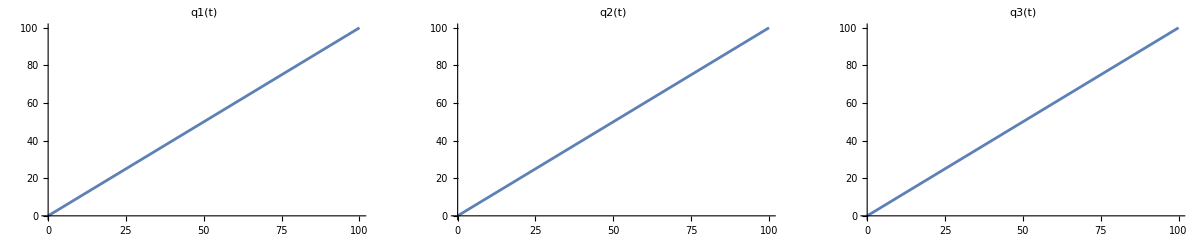

```mathematica
GraphicsRow[{P1,P2,P3}]
```

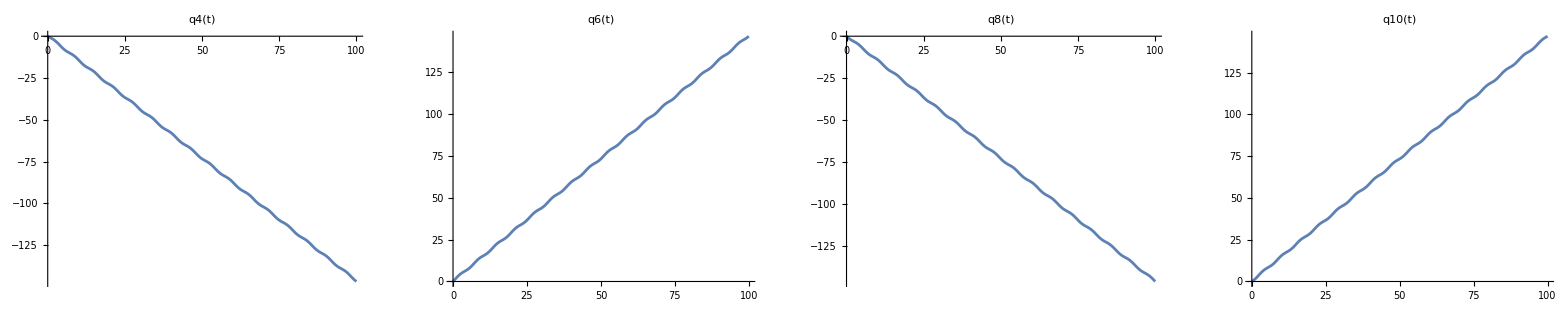

```mathematica
GraphicsRow[{P4,P6,P8,P10}]
```

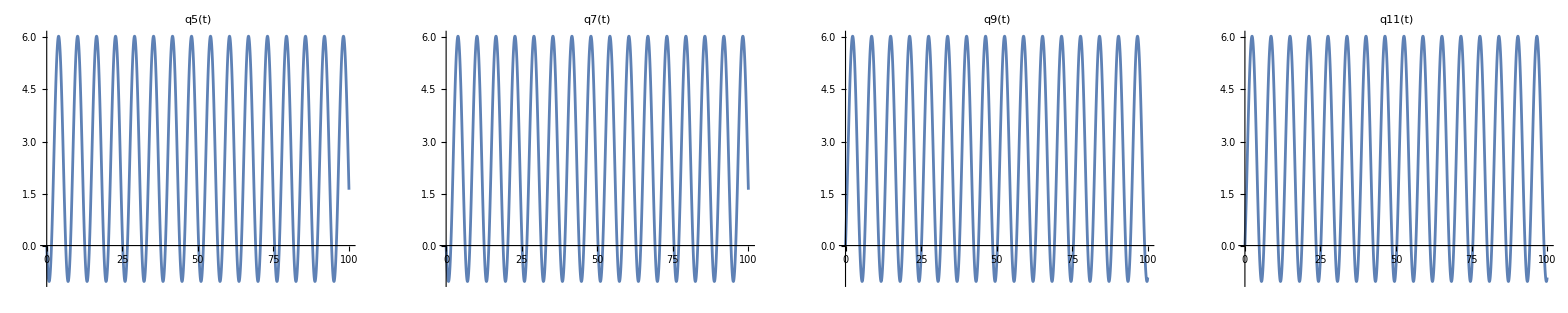

```mathematica
GraphicsRow[{P5,P7,P9,P11}]
```

#### Animation

Create functions for the coordinates for demonstration purposes.

```mathematica
A=8;
```

```mathematica
Subscript[q, 1][t_]:=q1sol
Subscript[q, 2][t_]:= q2sol
Subscript[q, 3][t_]:=q3sol
Subscript[q, 4][t_]:= q4sol
Subscript[q, 5][t_]:= q5sol
Subscript[q, 6][t_]:=q6sol
Subscript[q, 7][t_]:=q7sol
Subscript[q, 8][t_]:= q8sol
Subscript[q, 9][t_]:= q9sol
Subscript[q, 10][t_]:= q10sol
Subscript[q, 11][t_]:= q11sol
```

Create composite graphic out of parts that have been rotated and translated

```mathematica
robotGraphicAnim1={
(*Base graphic*)
Translate[GeometricTransformation[baseGraphic,Transpose[rotA]],{xA,yA,zA}],

(*Wheel graphic*)
Translate[GeometricTransformation[comwheelGraphic1,Transpose[rotB]],{xB,yB,zB}],
Translate[GeometricTransformation[barrelGraphic1,Transpose[rotC]],{xC,yC,zC}],
Translate[GeometricTransformation[comwheelGraphic2,Transpose[rotD]],{xD,yD,zD}],
Translate[GeometricTransformation[comwheelGraphic3,Transpose[rotF]],{xF,yF,zF}],
Translate[GeometricTransformation[comwheelGraphic4,Transpose[rotH]],{xH,yH,zH}]
};
```

Make it a function of to so it can be looped over time

```mathematica
robotGraphicAnimT1[t_]=robotGraphicAnim1;
(*NtPp[t_]=NtP;*)
```

```mathematica
tf=100;
scale=3A;
```

```mathematica
Animate[Show[Graphics3D[robotGraphicAnimT1[t],ViewPoint->{1,1,1},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->True,Axes->True,PlotRange->{{-scale,scale},{-scale,scale},{-scale,scale}},AspectRatio->1,AxesLabel->{"X","Y","Z"}],ImageSize->500](*,MatrixForm[NtPp[t]//N]*),{t,0,tf,tf/10000},AnimationRunning->False]
```

```mathematica
Animate[Show[Graphics3D[robotGraphicAnimT1[t],ViewPoint->{1,1,1},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->True,Axes->True,PlotRange->All,AspectRatio->1,AxesLabel->{"X","Y","Z"}],ImageSize->500](*,MatrixForm[NtPp[t]//N]*),{t,0,tf,tf/1000},AnimationRunning->False]
```

Assume the base is made form perspex (Density =1.18 g/cm.b3=1180kg/m3)and wheels from a nylon (Density =1.15 g/cm.b3=1150 kg/m3)

#### Manipulated FK animation

```mathematica
robotGraphicAnimT4[As_,b1_,b2_,b3_,tt_,tf_]:=Module[{qtsol,q1sol,q2sol,q3sol,q4sol,q5sol,q6sol,q7sol,q8sol,q9sol,q10sol,q11sol,A},
Subscript[q, 1][t_]=.;
Subscript[q, 2][t_]=.;
Subscript[q, 3][t_]=.;
Subscript[q, 4][t_]=.;
Subscript[q, 5][t_]=.;
Subscript[q, 6][t_]=.;
Subscript[q, 7][t_]=.;
Subscript[q, 8][t_]=.;
Subscript[q, 9][t_]=.;
Subscript[q, 10][t_]=.;
Subscript[q, 11][t_]=.;
qtsol=qt[b1,b2,b3,tt];
q1sol=Subscript[q, 1][t]/.qtsol;
q2sol=Subscript[q, 2][t]/.qtsol;
q3sol=Subscript[q, 3][t]/.qtsol;
q4sol=Subscript[q, 4][t]/.qtsol;
q5sol=Subscript[q, 5][t]/.qtsol;
q6sol=Subscript[q, 6][t]/.qtsol;
q7sol=Subscript[q, 7][t]/.qtsol;
q8sol=Subscript[q, 8][t]/.qtsol;
q9sol=Subscript[q, 9][t]/.qtsol;
q10sol=Subscript[q, 10][t]/.qtsol;
q11sol=Subscript[q, 11][t]/.qtsol;
A=As;
Subscript[q, 1][t_]:=q1sol;
Subscript[q, 2][t_]:= q2sol;
Subscript[q, 3][t_]:=q3sol;
Subscript[q, 4][t_]:= q4sol;
Subscript[q, 5][t_]:= q5sol;
Subscript[q, 6][t_]:=q6sol;
Subscript[q, 7][t_]:=q7sol;
Subscript[q, 8][t_]:= q8sol;
Subscript[q, 9][t_]:= q9sol;
Subscript[q, 10][t_]:= q10sol;
Subscript[q, 11][t_]:= q11sol;
Graphics3D[{
(*Base graphic*)
Translate[GeometricTransformation[baseGraphic,Transpose[rotA]],{xA,yA,zA}],

(*Wheel graphic*)
Translate[GeometricTransformation[comwheelGraphic1,Transpose[rotB]],{xB,yB,zB}],
Translate[GeometricTransformation[barrelGraphic1,Transpose[rotC]],{xC,yC,zC}],
Translate[GeometricTransformation[comwheelGraphic2,Transpose[rotD]],{xD,yD,zD}],
Translate[GeometricTransformation[comwheelGraphic3,Transpose[rotF]],{xF,yF,zF}],
Translate[GeometricTransformation[comwheelGraphic4,Transpose[rotH]],{xH,yH,zH}]
}//.t->tt]
]
```

```mathematica
Manipulate[Show[robotGraphicAnimT4[A,B1,B2,B3,t,tf],ViewPoint->{1,1,1},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->True,Axes->True,PlotRange->{{-scale,scale},{-scale,scale},{-scale,scale}},AspectRatio->1,AxesLabel->{"X","Y","Z"},ImageSize->500],{{t,1},0,tf,tf/500,Appearance->"Open"},{{B1,1},-5,5,1,Appearance->"Open"},{{B2,3},-5,5,1,Appearance->"Open"},{{B3,2},-5,5,1,Appearance->"Open"}]
```

## Inverse Kinematics

#### Clearing variables

```mathematica
Subscript[q, 1][t_]=.;
Subscript[q, 2][t_]=.;
Subscript[q, 3][t_]=.;
Subscript[q, 4][t_]=.;
Subscript[q, 5][t_]=.;
Subscript[q, 6][t_]=.;
Subscript[q, 7][t_]=.;
Subscript[q, 8][t_]=.;
Subscript[q, 9][t_]=.;
Subscript[q, 10][t_]=.;
Subscript[q, 11][t_]=.;
A=.;
B=.;
t=.;
Cc=.;
ω=.;
Ω=.;
r=.;
R=.;
A1=.;
A2=.;
A3=.;
B1=.;
B2=.;
B3=.;
```

Let’s Use Least square method

#### Least square method

```mathematica
relTransform[x_]:=x//.tRules
(*mytrig[x_]:= x/.{a__ Cos[b_]^2+a__ Sin[b_]^2-> a,a_. Cos[b_]^2+a_. Sin[b_]^2-> a}*)
```

```mathematica
MatrixA={{Coefficient[ω1a, Subscript[u, 1]],Coefficient[ω1a, Subscript[u, 2]],Coefficient[ω1a, Ω]},{Coefficient[ω2a, Subscript[u, 1]],Coefficient[ω2a, Subscript[u, 2]],Coefficient[ω2a, Ω]},{Coefficient[ω3a, Subscript[u, 1]],Coefficient[ω3a, Subscript[u, 2]],Coefficient[ω3a, Ω]},{Coefficient[ω4a, Subscript[u, 1]],Coefficient[ω4a, Subscript[u, 2]],Coefficient[ω4a, Ω]}}
```

{{(1. Cos[q_3[t]])/R,(1. Sin[q_3[t]])/R,-4.4/R},{(1. Cos[q_3[t]])/R,(1. Sin[q_3[t]])/R,4.4/R},{(1. Sin[q_3[t]])/R,-(1. Cos[q_3[t]])/R,-4.4/R},{(1. Sin[q_3[t]])/R,-(1. Cos[q_3[t]])/R,4.4/R}}

```mathematica
(*ωi={{ω1},{ω2},{ω3},{ω4}}*)
```

```mathematica
(*Q={{Subscript[u, 1]},{Subscript[u, 2]},{Ω}}*)
```

```mathematica
MatLeast=Inverse[Transpose[MatrixA].MatrixA].Transpose[MatrixA]//FullSimplify//Expand//gatherScalars//Chop(*//mytrig*)
```

{{0.5 R Cos[q_3[t]],0.5 R Cos[q_3[t]],0.5 R Sin[q_3[t]],0.5 R Sin[q_3[t]]},{0.5 R Sin[q_3[t]],0.5 R Sin[q_3[t]],-0.5 R Cos[q_3[t]],-0.5 R Cos[q_3[t]]},{-0.0568182 R,0.0568182 R,-0.0568182 R,0.0568182 R}}

```mathematica
(*Q=.;*)
```

```mathematica
MatLeastar=MatLeast(*/.{ω1-> Subscript[q, 4]'[t],ω2-> Subscript[q, 6]'[t],ω3-> Subscript[q, 8]'[t],ω4-> Subscript[q, 10]'[t]}*)//.{Subscript[q, n_][t]->Subscript[Q, n][t] ,Subscript[q, n_]'[t]->Subscript[Q, n]'[t] }//gatherScalars//Chop(*//mytrig*)
```

{{0.5 R Cos[Q_3[t]],0.5 R Cos[Q_3[t]],0.5 R Sin[Q_3[t]],0.5 R Sin[Q_3[t]]},{0.5 R Sin[Q_3[t]],0.5 R Sin[Q_3[t]],-0.5 R Cos[Q_3[t]],-0.5 R Cos[Q_3[t]]},{-0.0568182 R,0.0568182 R,-0.0568182 R,0.0568182 R}}

```mathematica
MatLeastar//MatrixForm
```

(0.5 R Cos[Q_3[t]] | 0.5 R Cos[Q_3[t]] | 0.5 R Sin[Q_3[t]] | 0.5 R Sin[Q_3[t]]
0.5 R Sin[Q_3[t]] | 0.5 R Sin[Q_3[t]] | -0.5 R Cos[Q_3[t]] | -0.5 R Cos[Q_3[t]]
-0.0568182 R | 0.0568182 R | -0.0568182 R | 0.0568182 R)

```mathematica
(*Subscript[Ui, Des]={{vx},{vy},{Ωz}}*)
```

```mathematica
A4= 0; A6= 0; A8= 0;A10= 0;
```

### q4 q6 q8 q10 pre -defined velocity

#### q4[t]

```mathematica
eqin1=Subscript[Q, 4]'[t]==A4 t+ B4
```

Q_4'[t]==B4

#### q6[t]

```mathematica
eqin2=Subscript[Q, 6]'[t]==A6 t+ B6
```

Q_6'[t]==B6

#### q8[t]

```mathematica
eqin3=Subscript[Q, 8]'[t]==A8 t+ B8
```

Q_8'[t]==B8

#### q10[t]

```mathematica
eqin4=Subscript[Q, 10]'[t]==A10 t+ B10
```

Q_10'[t]==B10

```mathematica
SetAttributes[{B4,B6,B8, B10},Constant]
```

### q1 q2 q3 calculating with the aid of q4 q6 q8 q10

#### Q1[t]

Comment these for the moment as testing

```mathematica
eqin5Right0=MatLeastar[[1]]//FullSimplify//Chop(*//mytrig*)
```

{0.5 R Cos[Q_3[t]],0.5 R Cos[Q_3[t]],0.5 R Sin[Q_3[t]],0.5 R Sin[Q_3[t]]}

```mathematica
eqin5Right1=eqin5Right0.{Subscript[Q, 4]'[t],Subscript[Q, 6]'[t],Subscript[Q, 8]'[t],Subscript[Q, 10]'[t]}//FullSimplify//Chop(*//mytrig*)
```

R (Cos[Q_3[t]] (0.5 Q_4'[t]+0.5 Q_6'[t])+Sin[Q_3[t]] (0.5 Q_8'[t]+0.5 Q_10'[t]))

```mathematica
eqin5=Subscript[Q, 1]'[t]==eqin5Right1//Chop(*//mytrig*)
```

Q_1'[t]==R (Cos[Q_3[t]] (0.5 Q_4'[t]+0.5 Q_6'[t])+Sin[Q_3[t]] (0.5 Q_8'[t]+0.5 Q_10'[t]))

#### Q2[t]

```mathematica
eqin6Right0=MatLeastar[[2]]//FullSimplify//Chop(*//mytrig*)
```

{0.5 R Sin[Q_3[t]],0.5 R Sin[Q_3[t]],-0.5 R Cos[Q_3[t]],-0.5 R Cos[Q_3[t]]}

```mathematica
eqin6Right1=eqin6Right0.{Subscript[Q, 4]'[t],Subscript[Q, 6]'[t],Subscript[Q, 8]'[t],Subscript[Q, 10]'[t]}//FullSimplify//Chop(*//mytrig*)
```

R (Sin[Q_3[t]] (0.5 Q_4'[t]+0.5 Q_6'[t])+Cos[Q_3[t]] (-0.5 Q_8'[t]-0.5 Q_10'[t]))

```mathematica
eqin6=Subscript[Q, 2]'[t]==eqin6Right1//Chop(*//mytrig*)
```

Q_2'[t]==R (Sin[Q_3[t]] (0.5 Q_4'[t]+0.5 Q_6'[t])+Cos[Q_3[t]] (-0.5 Q_8'[t]-0.5 Q_10'[t]))

#### Q3[t]

```mathematica
eqin7Right0=MatLeastar[[3]]//FullSimplify//Chop(*//mytrig*)
```

{-0.0568182 R,0.0568182 R,-0.0568182 R,0.0568182 R}

```mathematica
eqin7Right1=eqin7Right0.{Subscript[Q, 4]'[t],Subscript[Q, 6]'[t],Subscript[Q, 8]'[t],Subscript[Q, 10]'[t]}//FullSimplify//Chop(*//mytrig*)
```

R (-0.0568182 Q_4'[t]+0.0568182 Q_6'[t]-0.0568182 Q_8'[t]+0.0568182 Q_10'[t])

```mathematica
eqin7=Subscript[Q, 3]'[t]==eqin7Right1//Chop(*//mytrig*)
```

Q_3'[t]==R (-0.0568182 Q_4'[t]+0.0568182 Q_6'[t]-0.0568182 Q_8'[t]+0.0568182 Q_10'[t])

### q5 q7 q9 q11

#### Q5

```mathematica
eqQ5=eq5/.{Subscript[q, 1]'[t]-> Subscript[Q, 1]'[t],Subscript[q, 2]'[t]-> Subscript[Q, 2]'[t],Subscript[q, 3][t]-> Subscript[Q, 3][t],Subscript[q, 5]'[t]-> Subscript[Q, 5]'[t]}
```

Q_5'[t]==(Sin[Q_3[t]] Q_1'[t]-Cos[Q_3[t]] Q_2'[t])/r

#### Q7

```mathematica
eqQ7=eq6/.{Subscript[q, 1]'[t]-> Subscript[Q, 1]'[t],Subscript[q, 2]'[t]-> Subscript[Q, 2]'[t],Subscript[q, 3][t]-> Subscript[Q, 3][t],Subscript[q, 7]'[t]-> Subscript[Q, 7]'[t]}
```

Q_7'[t]==(Sin[Q_3[t]] Q_1'[t]-Cos[Q_3[t]] Q_2'[t])/r

#### Q9

```mathematica
eqQ9=eq7/.{Subscript[q, 1]'[t]-> Subscript[Q, 1]'[t],Subscript[q, 2]'[t]-> Subscript[Q, 2]'[t],Subscript[q, 3][t]-> Subscript[Q, 3][t],Subscript[q, 9]'[t]-> Subscript[Q, 9]'[t]}
```

Q_9'[t]==(Cos[Q_3[t]] Q_1'[t]+Sin[Q_3[t]] Q_2'[t])/r

#### Q11

```mathematica
eqQ11=eq8/.{Subscript[q, 1]'[t]-> Subscript[Q, 1]'[t],Subscript[q, 2]'[t]-> Subscript[Q, 2]'[t],Subscript[q, 3][t]-> Subscript[Q, 3][t],Subscript[q, 11]'[t]-> Subscript[Q, 11]'[t]}
```

Q_11'[t]==(Cos[Q_3[t]] Q_1'[t]+Sin[Q_3[t]] Q_2'[t])/r

### Equation

-Graphics3D-

```mathematica
(*eqQ5,eqQ7,eqQ9,eqQ11,*)
(*,Subscript[Q, 5][0]==0.1,Subscript[Q, 7][0]==0.1,Subscript[Q, 9][0]==0.1,Subscript[Q, 11][0]==0.1*)
```

ICns Q_4[0]==5,Q_6[0]==5.1,Q_8[0]==-5.1,Q_10[0]==-5

```mathematica
(*qtinv[b4_,b6_,b8_,b10_,Tfin_]:=NDSolve[{eqin1,eqin2,eqin3,eqin4,eqin5,eqin6,eqin7,Subscript[Q, 1][0]==0,Subscript[Q, 2][0]==0,Subscript[Q, 3][0]==0,Subscript[Q, 4][0]==1.5,Subscript[Q, 6][0]==1.51,Subscript[Q, 8][0]==-1.51,Subscript[Q, 10][0]==-1.5}/.{r-> 0.4,R->3,B4->b4,B6->b6,B8->b8,B10->b10,A4-> 0, A6-> 0, A8-> 0,A10-> 0},{Subscript[Q, 1][t],Subscript[Q, 2][t],Subscript[Q, 3][t],Subscript[Q, 4][t],Subscript[Q, 6][t],Subscript[Q, 8][t],Subscript[Q, 10][t]},{t,0, Tfin}]//First*)
```

```mathematica
qtinv[b4_,b6_,b8_,b10_,Tfin_]:=NDSolve[{eqin1,eqin2,eqin3,eqin4,eqin5,eqin6,eqin7,eqQ5,eqQ7,eqQ9,eqQ11, Subscript[Q, 1][0]==0,Subscript[Q, 2][0]==0,Subscript[Q, 3][0]==0,Subscript[Q, 4][0]==0,Subscript[Q, 6][0]==0,Subscript[Q, 8][0]==0,Subscript[Q, 10][0]==0,Subscript[Q, 5][0]==0,Subscript[Q, 7][0]==0,Subscript[Q, 9][0]==0,Subscript[Q, 11][0]==0}/.{r-> 0.4,R->3,B4->b4,B6->b6,B8->b8,B10->b10,A4-> 0, A6-> 0, A8-> 0,A10-> 0},{Subscript[Q, 1][t],Subscript[Q, 2][t],Subscript[Q, 3][t],Subscript[Q, 4][t],Subscript[Q, 6][t],Subscript[Q, 8][t],Subscript[Q, 10][t],Subscript[Q, 5][t],Subscript[Q, 7][t],Subscript[Q, 9][t],Subscript[Q, 11][t]},{t,0, Tfin}]//First
```

```mathematica
qtinvsol=.;
```

```mathematica
(*qtinvsol=qtinv[0.5,0.3,-0.1,-0.2,100]*)
```

```mathematica
qtinvsol=qtinv[0,0,-1,-1,100]
```

{Q_1[t]→InterpolatingFunction[…][t],Q_2[t]→InterpolatingFunction[…][t],Q_3[t]→InterpolatingFunction[…][t],Q_4[t]→InterpolatingFunction[…][t],Q_6[t]→InterpolatingFunction[…][t],Q_8[t]→InterpolatingFunction[…][t],Q_10[t]→InterpolatingFunction[…][t],Q_5[t]→InterpolatingFunction[…][t],Q_7[t]→InterpolatingFunction[…][t],Q_9[t]→InterpolatingFunction[…][t],Q_11[t]→InterpolatingFunction[…][t]}

### Results

#### Q1[t]

```mathematica
Subscript[Qn, 1][t]=Subscript[Q, 1][t]/.qtinvsol
```

InterpolatingFunction[…][t]

```mathematica
Qn1[t]=Subscript[Qn, 1][t]
```

InterpolatingFunction[…][t]

```mathematica
Q1plot=Plot[Qn1[t],{t,0,100}]
```

-Graphics-

#### Q2[t]

```mathematica
Subscript[Qn, 2][t_]=Subscript[Q, 2][t]/.qtinvsol
```

InterpolatingFunction[…][t]

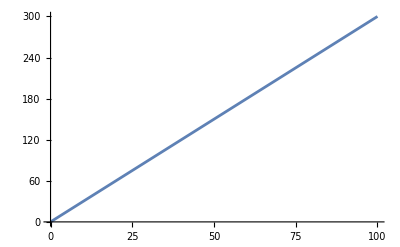

```mathematica
Qn2[t_]=Subscript[Qn, 2][t];
Q2plot=Plot[Qn2[t],{t,0,100}]
```

```mathematica
Manipulate[ParametricPlot[{Subscript[Q, 1][t]/.qtinvsol,Subscript[Q, 2][t]/.qtinvsol},{t,0,TF}],{TF,0.0001,100,50/10000}]
```

```mathematica
Subscript[Qn, 3][t_]=Subscript[Q, 3][t]/.qtinvsol
```

InterpolatingFunction[…][t]

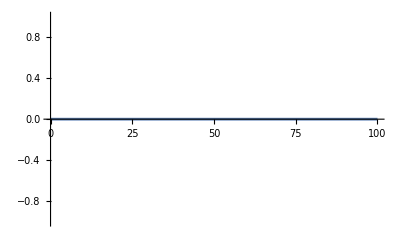

```mathematica
Qn3[t_]=Subscript[Qn, 3][t];
Q3plot=Plot[Qn3[t],{t,0,100}]
```

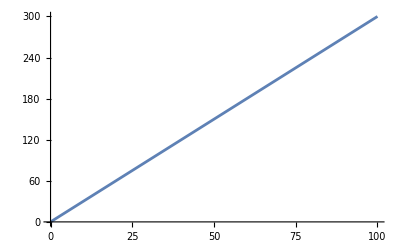

```mathematica
Show[Q1plot,Q2plot, PlotRange-> All]
```

#### Q1'[t]

```mathematica
Q1d[t_]=D[Subscript[Qn, 1][t],t]
```

InterpolatingFunction[…][t]

```mathematica
Q1dplot=Plot[Q1d[t],{t,0,100}, PlotRange-> All]
```

-Graphics-

#### Q2'[t]

```mathematica
Q2d[t_]=D[Subscript[Qn, 2][t],t]
```

InterpolatingFunction[…][t]

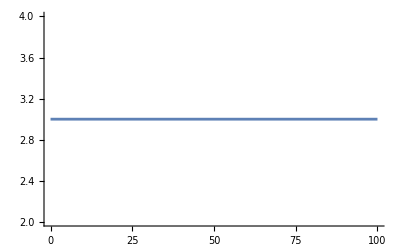

```mathematica
Q2dplot=Plot[Q2d[t],{t,0,100}, PlotRange-> All]
```

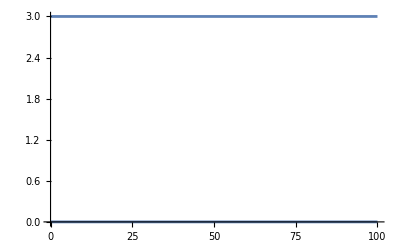

```mathematica
Show[Q1dplot,Q2dplot]
```

#### Q3’[t]

```mathematica
Q3d[t_]=D[Subscript[Qn, 3][t],t]
```

InterpolatingFunction[…][t]

```mathematica
Q3dplot=Plot[Q3d[t],{t,0,100}, PlotRange-> All]
```

-Graphics-

### Animation

Create functions for the coordinates for demonstration purposes.

```mathematica
A=8;
```

```mathematica
(*Subscript[q, n_][t_]:=Subscript[Q, n][t]*)
```

```mathematica
q1insol=Subscript[q, 1][t]/.{Subscript[q, 1][t]-> Subscript[Q, 1][t]}/.qtinvsol;
q2insol=Subscript[q, 2][t]/.{Subscript[q, 2][t]-> Subscript[Q, 2][t]}/.qtinvsol;
q3insol=Subscript[q, 3][t]/.{Subscript[q, 3][t]-> Subscript[Q, 3][t]}/.qtinvsol;
q4insol=Subscript[q, 4][t]/.{Subscript[q, 4][t]-> Subscript[Q, 4][t]}/.qtinvsol;
q5insol=Subscript[q, 5][t]/.{Subscript[q, 5][t]-> Subscript[Q, 5][t]}/.qtinvsol;
q6insol=Subscript[q, 6][t]/.{Subscript[q, 6][t]-> Subscript[Q, 6][t]}/.qtinvsol;
q7insol=Subscript[q, 7][t]/.{Subscript[q, 7][t]-> Subscript[Q, 7][t]}/.qtinvsol;
q8insol=Subscript[q, 8][t]/.{Subscript[q, 8][t]-> Subscript[Q, 8][t]}/.qtinvsol;
q9insol=Subscript[q, 9][t]/.{Subscript[q, 9][t]-> Subscript[Q, 9][t]}/.qtinvsol;
q10insol=Subscript[q, 10][t]/.{Subscript[q, 10][t]-> Subscript[Q, 10][t]}/.qtinvsol;
q11insol=Subscript[q, 11][t]/.{Subscript[q, 11][t]-> Subscript[Q, 11][t]}/.qtinvsol;
```

```mathematica
Subscript[q, 1][t_]:=q1insol
Subscript[q, 2][t_]:= q2insol
Subscript[q, 3][t_]:=q3insol
Subscript[q, 4][t_]:= q4insol
Subscript[q, 5][t_]:= q5insol
Subscript[q, 6][t_]:=q6insol
Subscript[q, 7][t_]:=q7insol
Subscript[q, 8][t_]:= q8insol
Subscript[q, 9][t_]:= q9insol
Subscript[q, 10][t_]:= q10insol
Subscript[q, 11][t_]:= q11insol
```

Create composite graphic out of parts that have been rotated and translated

```mathematica
(*Subscript[q, n_][t_]:=Subscript[Q, n][t]*)
```

```mathematica
robotGraphicAnim2={
(*Base graphic*)
Translate[GeometricTransformation[baseGraphic,Transpose[rotA]],{xA,yA,zA}],

(*Wheel graphic*)
Translate[GeometricTransformation[comwheelGraphic1,Transpose[rotB]],{xB,yB,zB}],
Translate[GeometricTransformation[barrelGraphic1,Transpose[rotC]],{xC,yC,zC}],
Translate[GeometricTransformation[comwheelGraphic2,Transpose[rotD]],{xD,yD,zD}],
Translate[GeometricTransformation[comwheelGraphic3,Transpose[rotF]],{xF,yF,zF}],
Translate[GeometricTransformation[comwheelGraphic4,Transpose[rotH]],{xH,yH,zH}]
};
```

Make it a function of to so it can be looped over time

```mathematica
robotGraphicAnimT2[t_]=robotGraphicAnim2;
(*NtPp[t_]=NtP;*)
```

```mathematica
tf=100;
scale=3A;
```

```mathematica
Animate[Show[Graphics3D[robotGraphicAnimT2[t],ViewPoint->{1,1,1},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->True,Axes->True,PlotRange->{{-scale,scale},{-scale,scale},{-scale,scale}},AspectRatio->1,AxesLabel->{"X","Y","Z"}],ImageSize->500](*,MatrixForm[NtPp[t]//N]*),{t,0,tf,tf/500},AnimationRunning->False]
```

```mathematica
Animate[Show[Graphics3D[robotGraphicAnimT2[t],ViewPoint->{1,1,1},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->True,Axes->True,PlotRange->All,AspectRatio->1,AxesLabel->{"X","Y","Z"}],ImageSize->500](*,MatrixForm[NtPp[t]//N]*),{t,0,tf,tf/1000},AnimationRunning->False]
```

Assume the base is made form perspex (Density =1.18 g/cm.b3=1180kg/m3)and wheels from a nylon (Density =1.15 g/cm.b3=1150 kg/m3)

### Manipulated IK animation

```mathematica
robotGraphicAnimT3[As_,b1_,b2_,b3_,b4_,tt_,tf_]:=Module[{qtinvsol,q1insol,q2insol,q3insol,q4insol,q5insol,q6insol,q7insol,q8insol,q9insol,q10insol,q11insol,A},
Subscript[q, 1][t_]=.;
Subscript[q, 2][t_]=.;
Subscript[q, 3][t_]=.;
Subscript[q, 4][t_]=.;
Subscript[q, 5][t_]=.;
Subscript[q, 6][t_]=.;
Subscript[q, 7][t_]=.;
Subscript[q, 8][t_]=.;
Subscript[q, 9][t_]=.;
Subscript[q, 10][t_]=.;
Subscript[q, 11][t_]=.;
qtinvsol=qtinv[b1,b2,b3,b4,tt];
q1insol=Subscript[Q, 1][t]/.qtinvsol;
q2insol=Subscript[Q, 2][t]/.qtinvsol;
q3insol=Subscript[Q, 3][t]/.qtinvsol;
q4insol=Subscript[Q, 4][t]/.qtinvsol;
q5insol=Subscript[Q, 5][t]/.qtinvsol;
q6insol=Subscript[Q, 6][t]/.qtinvsol;
q7insol=Subscript[Q, 7][t]/.qtinvsol;
q8insol=Subscript[Q, 8][t]/.qtinvsol;
q9insol=Subscript[Q, 9][t]/.qtinvsol;
q10insol=Subscript[Q, 10][t]/.qtinvsol;
q11insol=Subscript[Q, 11][t]/.qtinvsol;
A=As;
Subscript[q, 1][t_]:=q1insol;
Subscript[q, 2][t_]:= q2insol;
Subscript[q, 3][t_]:=q3insol;
Subscript[q, 4][t_]:= q4insol;
Subscript[q, 5][t_]:= q5insol;
Subscript[q, 6][t_]:=q6insol;
Subscript[q, 7][t_]:=q7insol;
Subscript[q, 8][t_]:= q8insol;
Subscript[q, 9][t_]:= q9insol;
Subscript[q, 10][t_]:= q10insol;
Subscript[q, 11][t_]:= q11insol;
Graphics3D[{
(*Base graphic*)
Translate[GeometricTransformation[baseGraphic,Transpose[rotA]],{xA,yA,zA}],

(*Wheel graphic*)
Translate[GeometricTransformation[comwheelGraphic1,Transpose[rotB]],{xB,yB,zB}],
Translate[GeometricTransformation[barrelGraphic1,Transpose[rotC]],{xC,yC,zC}],
Translate[GeometricTransformation[comwheelGraphic2,Transpose[rotD]],{xD,yD,zD}],
Translate[GeometricTransformation[comwheelGraphic3,Transpose[rotF]],{xF,yF,zF}],
Translate[GeometricTransformation[comwheelGraphic4,Transpose[rotH]],{xH,yH,zH}]
}//.t->tt]
]
```

```mathematica
Manipulate[Show[robotGraphicAnimT3[A,B1,B2,B3,B4,t,tf],ViewPoint->{1,1,1},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->True,Axes->True,PlotRange->{{-scale,scale},{-scale,scale},{-scale,scale}},AspectRatio->1,AxesLabel->{"X","Y","Z"},ImageSize->500],{{t,1},0,tf,tf/500,Appearance->"Open"},{{B1,1},-5,5,1,Appearance->"Open"},{{B2,3},-5,5,1,Appearance->"Open"},{{B3,2},-5,5,1,Appearance->"Open"},{{B4,2},-5,5,1,Appearance->"Open"}]
```

## continue to notebook part 2